```mathematica
Y=xs Cos[theta]+(r0+ys) Sin[theta]-xd;
X=(r0+xs)Cos[theta]+ys Sin[theta]-xd;
k1=-0.005;
k2=11.631;
k3=0.005;
k4=0.012;
k5=-17.195;
k6=0;
k7=0.082;
k8=-0.008;
k9=7.429;
k10=0;
arctg=k1 X^3+k2 X^2 Y+k3 X^2+k4 X Y^2+k5 X Y +k6 X +k7 Y^3+k8 Y^2 +k9 Y+k10;
TrigReduce[arctg];
prviHarmonik=(-0.103 r0-0.11925 r0^3+16.844 r0 xd+22.841 r0 xd^2)^2+(7.433r0+2.98675 r0^3+16.9772 r0 xd+11.593 r0 xd^2)^2;
drugiHarmonik=Sqrt[(0.0343 r0^2+-5.624 r0^2 xd)^2+(-8.612 r0^2-11.4824 r0^2 xd)^2];
tretjiHarmonik=Sqrt[(0.01925 r0^3)^2+(2.89075 r0^2)^2];
offset=0.014+0.1577 r0^2-7.33 xd-5.735 r0^2 xd-16.9086 xd^2-11.478000000000002 xd^3;

FullSimplify[prviHarmonik]
FullSimplify[drugiHarmonik]
FullSimplify[tretjiHarmonik]
FullSimplify[offset]
```

```mathematica
Y=0Cos[theta]+(r0+0) Sin[theta]-xd;
X=(r0+0)Cos[theta]+0 Sin[theta]-xd;
arctg=k1 X^3+k2 X^2 Y+k3 X^2+k4 X Y^2+k5 X Y +k6 X +k7 Y^3+k8 Y^2 +k9 Y+k10;lexd=FullSimplify[TrigReduce[arctg]]
```

r0^2 (-0.0015-5.937 xd)+xd (-7.429+(-17.198-11.72 xd) xd)+r0 Cos[theta] (-0.00075 r0^2+xd (17.185+23.259 xd)+r0 (-17.195-23.286 xd) Sin[theta])+r0 (r0 (0.0065-5.679 xd) Cos[2 theta]-0.00425 r0^2 Cos[3 theta]+(7.429+2.96925 r0^2+xd (17.211+11.901 xd)) Sin[theta]+2.88725 r0^2 Sin[3 theta])

```mathematica
Y=0 Cos[theta]+(r0+ys) Sin[theta]-0;
X=(r0+0)Cos[theta]+ys Sin[theta]-0;
arctg=k1 X^3+k2 X^2 Y+k3 X^2+k4 X Y^2+k5 X Y +k6 X +k7 Y^3+k8 Y^2 +k9 Y+k10;leys=FullSimplify[TrigReduce[arctg]]
```

-0.0015 r0^2-8.6055 r0 ys-8.599 ys^2+(0.0065 r0^2+8.6055 r0 ys+8.599 ys^2) Cos[2 theta]+r0 (-0.00425 r0^2-5.8215 r0 ys-5.81475 ys^2) Cos[3 theta]+(7.429 r0+2.96925 r0^3+7.429 ys+3.0975 r0^2 ys+8.92575 r0 ys^2+8.79 ys^3) Sin[theta]+r0 Cos[theta] (-0.00075 r0^2+5.8215 r0 ys+5.81475 ys^2+(-17.195 r0-17.185 ys) Sin[theta])+(2.88725 r0^3+2.8395 r0^2 ys-2.97525 r0 ys^2-2.93 ys^3) Sin[3 theta]

```mathematica
Y=xs Cos[theta]+(r0+0) Sin[theta]-0;
X=(r0+xs)Cos[theta]+0 Sin[theta]-0;
arctg=k1 X^3+k2 X^2 Y+k3 X^2+k4 X Y^2+k5 X Y +k6 X +k7 Y^3+k8 Y^2 +k9 Y+k10;lexs=Simplify[TrigReduce[arctg]]
```

-0.0015 r0^2-8.5925 r0 xs-8.599 xs^2+(0.0065 r0^2-8.5925 r0 xs-8.599 xs^2) Cos[2 theta]-0.00425 r0^3 Cos[3 theta]+2.8395 r0^2 xs Cos[3 theta]+5.81475 r0 xs^2 Cos[3 theta]+2.93 xs^3 Cos[3 theta]+7.429 r0 Sin[theta]+2.96925 r0^3 Sin[theta]+5.8215 r0^2 xs Sin[theta]+2.97525 r0 xs^2 Sin[theta]+Cos[theta] (-0.00075 r0^3+7.429 xs+8.7765 r0^2 xs+17.4443 r0 xs^2+8.79 xs^3+r0 (-17.195 r0-17.211 xs) Sin[theta])+2.88725 r0^3 Sin[3 theta]+5.8215 r0^2 xs Sin[3 theta]+2.97525 r0 xs^2 Sin[3 theta]

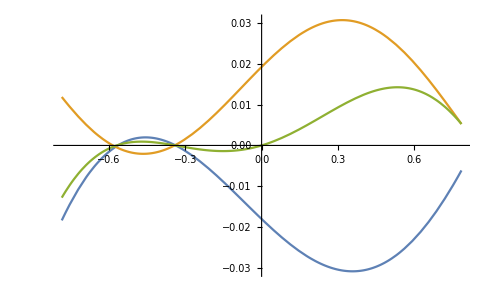

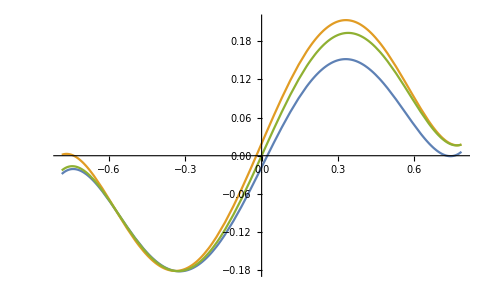

```mathematica
osnovnaNapaka=-0.0015+0.006500000000000001 Cos[2 theta]-0.00425 Cos[3 theta]+Cos[theta] (-0.0007499999999999998-17.195 Sin[theta])+10.39825 Sin[theta]+2.88725 Sin[3 theta]-theta;
xd=0.01;
xs=0.01;
ys=0.01;
r0=1;

Plot[{lexd-theta-osnovnaNapaka,lexs-theta-osnovnaNapaka,leys-theta-osnovnaNapaka},{theta,-Pi/4,Pi/4}]
Plot[{lexd-theta-0,lexs-theta-0,leys-theta-0},{theta,-Pi/4,Pi/4}]
```

```mathematica
osnovnaNapaka=-0.0015+0.006500000000000001 Cos[2 theta]-0.00425 Cos[3 theta]+Cos[theta] (-0.0007499999999999998-17.195 Sin[theta])+10.39825 Sin[theta]+2.88725 Sin[3 theta];
```

```mathematica
Simplify[(r th -xd)/(r0-xd)+(r th -xd)^3/(3(r -xd)^3)]
```

(r th-xd)/(r0-xd)+(r th-xd)^3/(3 (r-xd)^3)

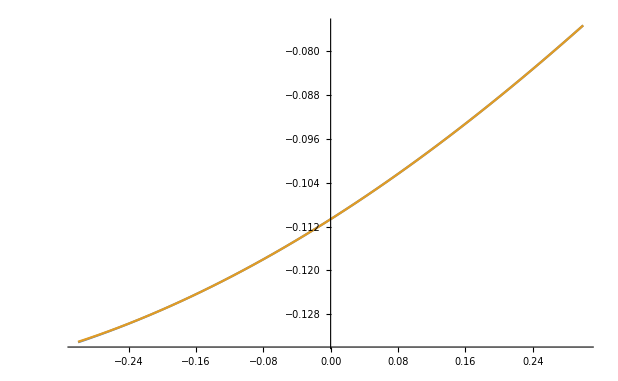

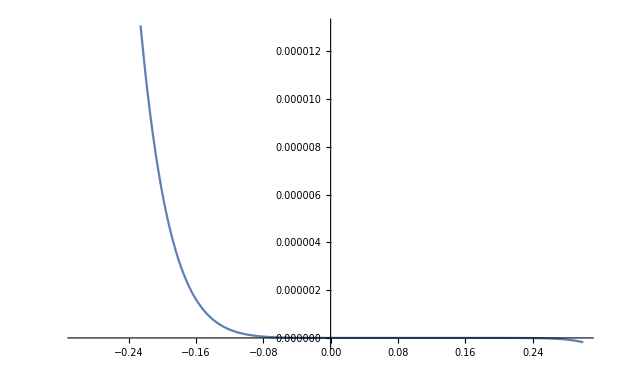

```mathematica
r0=1;
xd=0.1;
Plot[{ArcTan[(r0 Sin[θ]-xd)/(r0 Cos[θ]-xd)]-θ,(r0 Sin[θ]-xd)/(r0 Cos[θ]-xd)-1/3((r0 Sin[θ]-xd)/(r0 Cos[θ]-xd))^3+1/5((r0 Sin[θ]-xd)/(r0 Cos[θ]-xd))^5-1/7((r0 Sin[θ]-xd)/(r0 Cos[θ]-xd))^7-θ},{θ,-0.3,0.3}]
Plot[(r0 Sin[θ]-xd)/(r0 Cos[θ]-xd)-1/3((r0 Sin[θ]-xd)/(r0 Cos[θ]-xd))^3+1/5((r0 Sin[θ]-xd)/(r0 Cos[θ]-xd))^5-1/7((r0 Sin[θ]-xd)/(r0 Cos[θ]-xd))^7-ArcTan[(r0 Sin[θ]-xd)/(r0 Cos[θ]-xd)],{θ,-0.3,0.3}]
```